z-7 weak strong

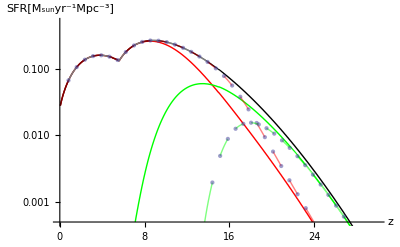

z-17 weak strong

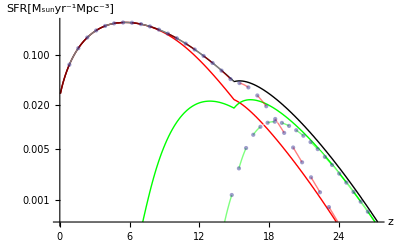

z-7 pop3 fit

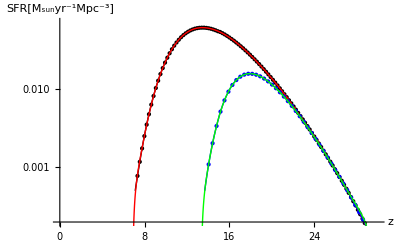

z-17 pop3 fit

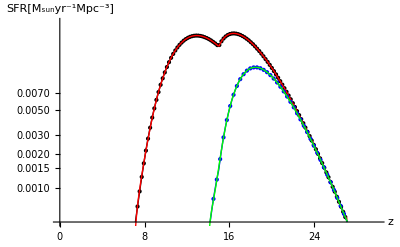

z-7 pop1 fit

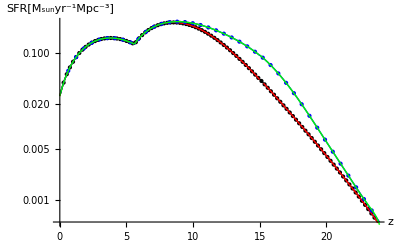

z-17 pop1 fit

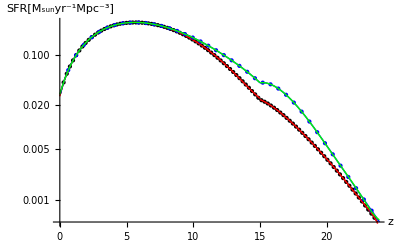

pop3 fit

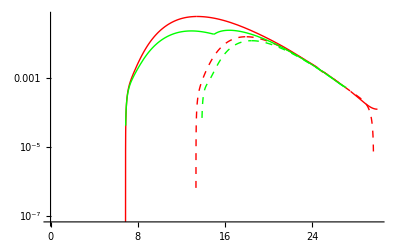

```mathematica
"z-7 weak strong"
Show[ListLogPlot[{z7pop1w,z7pop3w,z7tot},Joined->{True,True,True},PlotStyle->{Red,Green,Black}],ListLogPlot[{z7pop1s},Joined->True,PlotStyle->Directive[Opacity[0.5],Thick],Mesh->30,MeshFunctions->{#1&},MeshShading->{Red,White}],ListLogPlot[{z7pop3s},Joined->True,PlotStyle->Directive[Opacity[0.5],Thick],Mesh->20,MeshFunctions->{#1&},MeshShading->{Green,White}],
AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"},BaselinePosition->Axis,AxesOrigin->{0,Log[0.0005]},PlotRange-> {{0,30},{Log[0.0005],Log[0.5]}}]
"z-17 weak strong"
Show[ListLogPlot[{z17pop1w,z17pop3w,z17tot},Joined->{True,True,True},PlotStyle->{Red,Green,Black}],ListLogPlot[{z17pop1s},Joined->True,PlotStyle->Directive[Opacity[0.5],Thick],Mesh->30,MeshFunctions->{#1&},MeshShading->{Red,White}],ListLogPlot[{z17pop3s},Joined->True,PlotStyle->Directive[Opacity[0.5],Thick],Mesh->20,MeshFunctions->{#1&},MeshShading->{Green,White}],
AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}]

"z-7 pop3 fit"
Show[ListLogPlot[z7pop3w,Joined->True,Mesh->100,PlotStyle-> Black],LogPlot[z7pop3wf[x],{x,0,30},PlotStyle->Red],ListLogPlot[z7pop3s,Joined->True,Mesh->40,PlotStyle-> Blue],LogPlot[z7pop3sf[x],{x,0,30},PlotStyle->{Green}],AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}
,AxesOrigin->{0,Log[0.0002]},PlotRange-> {{0,30},{Log[0.0002],Log[0.07]}}]
"z-17 pop3 fit"
Show[ListLogPlot[z17pop3w,Joined->True,Mesh->100,PlotStyle-> Black],LogPlot[z17pop3wf[x],{x,0,30},PlotStyle->{Red}],ListLogPlot[z17pop3s,Joined->True,Mesh->40,PlotStyle-> Blue],LogPlot[z17pop3sf[x],{x,0,30},PlotStyle->{Green}],AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}
,AxesOrigin->{0,Log[0.0005]},PlotRange-> {{0,30},{Log[0.0005],Log[0.03]}}]
"z-7 pop1 fit"
Show[ListLogPlot[z7pop1w,Joined->True,Mesh->100,PlotStyle-> Black],LogPlot[z7pop1wf[x],{x,0,30},PlotStyle->Red],ListLogPlot[z7pop1s,Joined->True,Mesh->40,PlotStyle-> Blue],LogPlot[z7pop1sf[x],{x,0,30},PlotStyle->{Green}],AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}]
"z-17 pop1 fit"
Show[ListLogPlot[z17pop1w,Joined->True,Mesh->100,PlotStyle-> Black],LogPlot[z17pop1wf[x],{x,0,30},PlotStyle->{Red}],ListLogPlot[z17pop1s,Joined->True,Mesh->40,PlotStyle-> Blue],LogPlot[z17pop1sf[x],{x,0,30},PlotStyle->{Green}],AxesLabel->{z,"SFR[M_sunyr^-1Mpc^-3]"}]
"pop3 fit"
Show[LogPlot[z7pop3wf[z],{z,0,30},PlotStyle->{Red}],LogPlot[z7pop3sf[z],{z,0,30},PlotStyle->{Red,Dashed}],LogPlot[z17pop3wf[z],{z,0,30},PlotStyle->{Green}],LogPlot[z17pop3sf[z],{z,0,30},PlotStyle->{Green,Dashed}]]
```

IMF

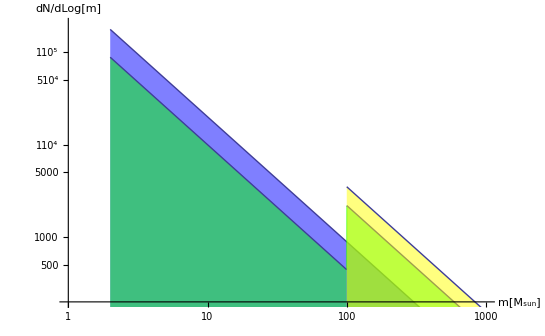

```mathematica
"IMF"
Show[LogLogPlot[IMF[m,coa,1.35,cob,1.35,Mt,mp1,mp2,1,1],{m,1,1000},Filling->Axis,FillingStyle->Directive[Opacity[0.5],Blue]],LogLogPlot[IMF[m,coa,1.35,cob,1.35,Mt,mp1,mp2,0.5,1],{m,1,1000},Filling->Axis,FillingStyle->Directive[Opacity[0.5],Green]],LogLogPlot[IMF[m,coa,1.35,cob,1.35,Mt,mp1,mp2,0,1],{m,1,1000},Filling->Axis,FillingStyle->Directive[Opacity[0.5],Yellow]],AxesLabel->{"m[M_sun]","dN/dLog[m]"},PlotRange->{{Log[1],Log[1000]},{Log[200],Log[2*^5]}},AxesOrigin->{Log[1],Log[200]}]
```

Integrated IMF

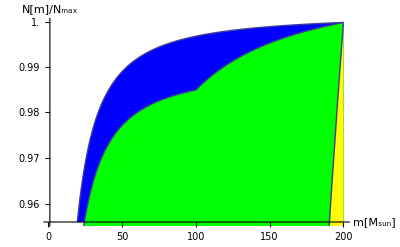

```mathematica
IIMF1=NIntegrate[IMF[mi,coa,1.35,cob,1.35,Mt,mp1,mp2,1,1]/mi,{mi,1,200}];
IIMF05=NIntegrate[IMF[mi,coa,1.35,cob,1.35,Mt,mp1,mp2,0.5,1]/mi,{mi,1,200}];
IIMF0=NIntegrate[IMF[mi,coa,1.35,cob,1.35,Mt,mp1,mp2,0,1]/mi,{mi,1,200}];
"Integrated IMF"
Show[LogPlot[NIntegrate[IMF[mi,coa,1.35,cob,1.35,Mt,mp1,mp2,1,1]/mi,{mi,1,m}]/IIMF1,{m,1,200},Filling->Axis,FillingStyle->Directive[Opacity[1],Blue]],LogPlot[NIntegrate[IMF[mi,coa,1.35,cob,1.35,Mt,mp1,mp2,0.5,1]/mi,{mi,1,m}]/IIMF05,{m,1,200},Filling->Axis,FillingStyle->Directive[Opacity[1],Green]],LogPlot[NIntegrate[IMF[mi,coa,1.35,cob,1.35,Mt,mp1,mp2,0,1]/mi,{mi,1,m}]/IIMF0,{m,1,200},Filling->Axis,FillingStyle->Directive[Opacity[1],Yellow]],AxesLabel->{"m[M_sun]","N[m]/N_max"}]
```

luminosity distance with redshift

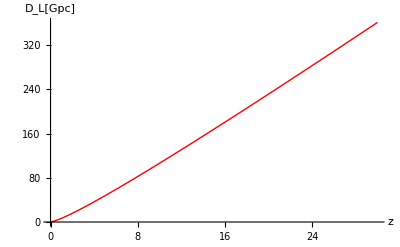

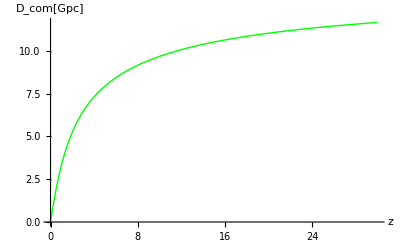

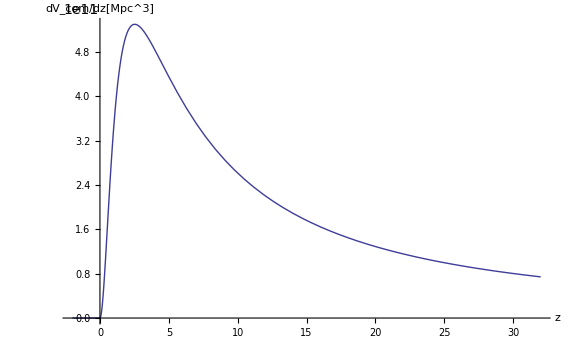

```mathematica
"luminosity distance with redshift"
Plot[dLf[z]/1000,{z,0,30},PlotStyle->Red,AxesLabel->{"z","D_L[Gpc]"},AxesOrigin->{0,0}]
Plot[Dcom[z]/1000,{z,0,30},PlotStyle->Green,AxesLabel->{"z","D_com[Gpc]"},AxesOrigin->{0,0}]
Plot[DVcom[z],{z,-2,32},AxesLabel->{z,"dV_com/dz[Mpc^3]"}]
```

GRB coefficients

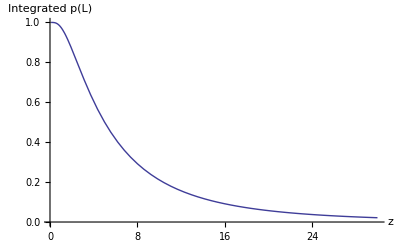

```mathematica
"GRB coefficients"
Plot[plall[z],{z,0.1,30},AxesLabel->{z,"Integrated p(L)"}]
```

InterpolatingFunction::dmval: Input value {-6.90754} lies outside the range of data in the interpolating function. Extrapolation will be used.

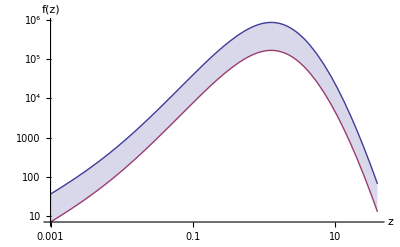

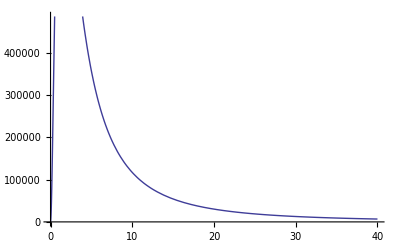

```mathematica
LogLogPlot[{fsimp3CEup[z],fsimp3CEdown[z]},{z,0.001,40},Filling->{1->{2}},AxesLabel->{"z","f(z)"}]
```

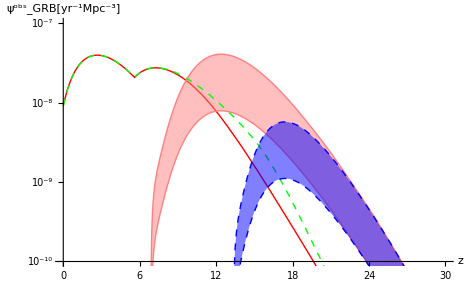

```mathematica
(*population I/II/III z-7 GRB CE rate*)
Show[LogPlot[GRBp1CE[z]*z7pop1wf[z],{z,0,30},PlotStyle->Red],LogPlot[{GRBp3CEup[z]*z7pop3wf[z],GRBp3CEdown[z]*z7pop3wf[z]},{z,0,30},PlotStyle->Pink,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink]],LogPlot[GRBp1CE[z]*z7pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],LogPlot[{GRBp3CEup[z]*z7pop3sf[z],GRBp3CEdown[z]*z7pop3sf[z]},{z,0,30},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],PlotStyle->{{Blue,Dashed},{Blue,Dashed}}],PlotRange->{{0,30},{Log[1*^-10],Log[1*^-7]}},AxesOrigin->{0,Log[1*^-10]},AxesLabel->{z,"(ψ^obs)_GRB[yr^-1Mpc^-3]"}]
```

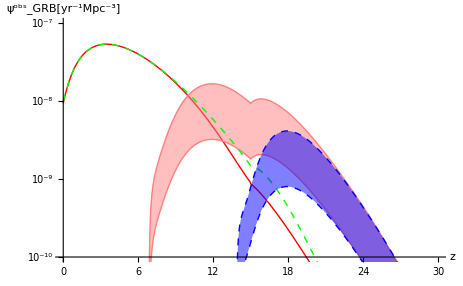

```mathematica
(*population I/II/III z-17 GRB CE rate*)
Show[LogPlot[GRBp1CE[z]*z17pop1wf[z],{z,0,30},PlotStyle->Red],LogPlot[{GRBp3CEup[z]*z17pop3wf[z],GRBp3CEdown[z]*z17pop3wf[z]},{z,0,30},PlotStyle->Pink,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink]],LogPlot[GRBp1CE[z]*z17pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],LogPlot[{GRBp3CEup[z]*z17pop3sf[z],GRBp3CEdown[z]*z17pop3sf[z]},{z,0,30},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],PlotStyle->{{Blue,Dashed},{Blue,Dashed}}],PlotRange->{{0,30},{Log[1*^-10],Log[1*^-7]}},AxesOrigin->{0,Log[1*^-10]},AxesLabel->{z,"(ψ^obs)_GRB[yr^-1Mpc^-3]"}]
```

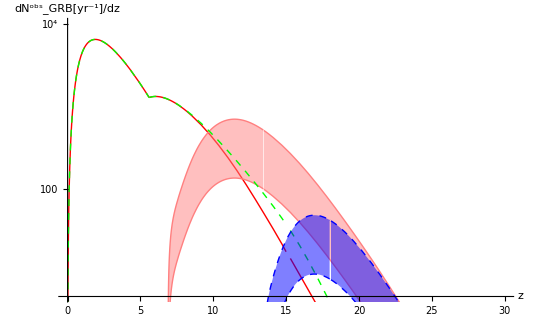

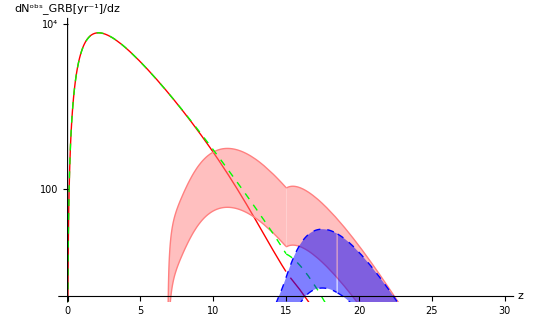

```mathematica
(*z-7 f(z)*)
Show[LogPlot[fsimp1CE[z]*z7pop1wf[z],{z,0,30},PlotStyle->Red],LogPlot[{fsimp3CEup[z]*z7pop3wf[z],fsimp3CEdown[z]*z7pop3wf[z]},{z,0,30},PlotStyle->Pink,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink]],LogPlot[fsimp1CE[z]*z7pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],LogPlot[{fsimp3CEup[z]*z7pop3sf[z],fsimp3CEdown[z]*z7pop3sf[z]},{z,0,30},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],PlotStyle->{{Blue,Dashed},{Blue,Dashed}}],AxesLabel->{z,"(dN^obs)_GRB[yr^-1]/dz"},AxesOrigin->{0,Log[5]},PlotRange->{{0,30},{Log[5],Log[10000]}}]
(*z-17 f(z)*)
Show[LogPlot[fsimp1CE[z]*z17pop1wf[z],{z,0,30},PlotStyle->Red],LogPlot[{fsimp3CEup[z]*z17pop3wf[z],fsimp3CEdown[z]*z17pop3wf[z]},{z,0,30},PlotStyle->Pink,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink]],LogPlot[fsimp1CE[z]*z17pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],LogPlot[{fsimp3CEup[z]*z17pop3sf[z],fsimp3CEdown[z]*z17pop3sf[z]},{z,0,30},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],PlotStyle->{{Blue,Dashed},{Blue,Dashed}}],AxesLabel->{z,"(dN^obs)_GRB[yr^-1]/dz"},AxesOrigin->{0,Log[5]},PlotRange->{{0,30},{Log[5],Log[10000]}}]
```

```mathematica
(*z-7 iso f(z)*)
Show[LogPlot[fisosimp1CE[z]*z7pop1wf[z],{z,0,30},PlotStyle->Red],LogPlot[{fisosimp3CEup[z]*z7pop3wf[z],fisosimp3CEdown[z]*z7pop3wf[z]},{z,0,30},PlotStyle->Pink,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink]],LogPlot[fisosimp1CE[z]*z7pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],LogPlot[{fisosimp3CEup[z]*z7pop3sf[z],fisosimp3CEdown[z]*z7pop3sf[z]},{z,0,30},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],PlotStyle->{{Blue,Dashed},{Blue,Dashed}}],AxesLabel->{z,"dN_GRB[yr^-1]/dz"},AxesOrigin->{0,Log[5]},PlotRange->{{0,30},{Log[5],Log[10000]}}]
(*z-17 f(z)*)
Show[LogPlot[fisosimp1CE[z]*z17pop1wf[z],{z,0,30},PlotStyle->Red],LogPlot[{fisosimp3CEup[z]*z17pop3wf[z],fisosimp3CEdown[z]*z17pop3wf[z]},{z,0,30},PlotStyle->Pink,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink]],LogPlot[fisosimp1CE[z]*z17pop1sf[z],{z,0,30},PlotStyle->{Green,Dashed}],LogPlot[{fisosimp3CEup[z]*z17pop3sf[z],fisosimp3CEdown[z]*z17pop3sf[z]},{z,0,30},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],PlotStyle->{{Blue,Dashed},{Blue,Dashed}}],AxesLabel->{z,"dN_GRB[yr^-1]/dz"},AxesOrigin->{0,Log[5]},PlotRange->{{0,30},{Log[5],Log[10000]}}]
```

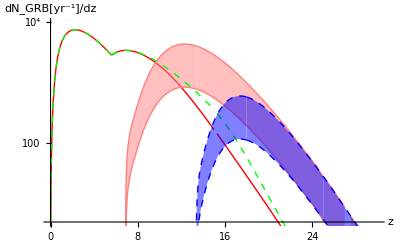

-Graphics-

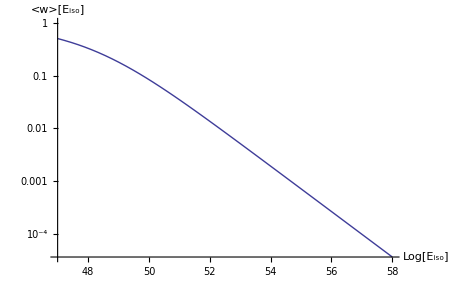

-Graphics-

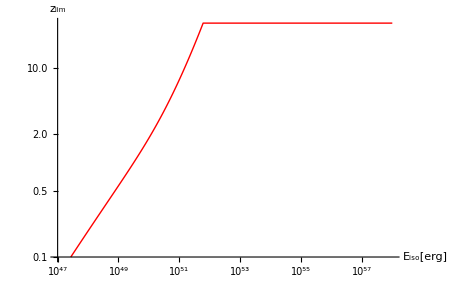

```mathematica
LogPlot[Averagew[x],{x,47,58},AxesLabel->{"Log[E_iso]","<w>[E_iso]"}]
Plot[4π*Dcom[z]^2*(1+z)*Fbollim,{z,0,30},AxesLabel->{z,"E_(iso . lim)[erg]"}]
ListLogLogPlot[zlim,PlotStyle->Red,Joined->True,AxesLabel->{"E_iso[erg]","z_lim"},PlotRange->{{10^47,10^58},{Log[5*^-5],Log[10^30]}}]
```

z-7

InterpolatingFunction::dmval: Input value {46.0003} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

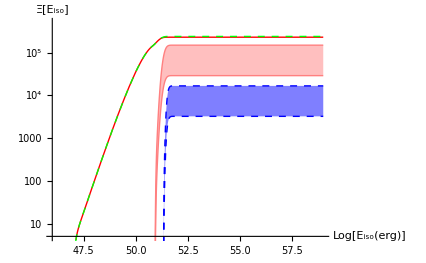

z-17

InterpolatingFunction::dmval: Input value {46.0003} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

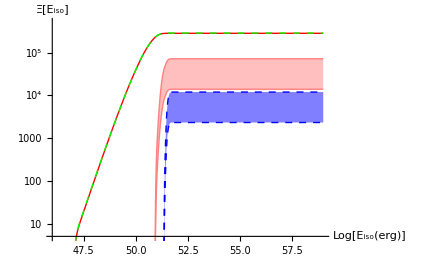

```mathematica
"z-7"
Show[LogPlot[Ξ7wfitcorp1CE[x]/ηbeaming/100,{x,46,59},PlotStyle->Red,PlotRange->All],LogPlot[{Ξ7wfitcorp3CEup[x]/ηbeaming/100,Ξ7wfitcorp3CEdown[x]/ηbeaming/100},{x,46,59},PlotStyle->Pink,PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink],AxesOrigin->{46,Log[5]}],LogPlot[Ξ7sfitcorp1CE[x]/ηbeaming/100,{x,46,59},PlotStyle->{Green,Dashed}],LogPlot[{Ξ7sfitcorp3CEup[x]/ηbeaming/100,Ξ7sfitcorp3CEdown[x]/ηbeaming/100},{x,46,59},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},PlotStyle->{Blue,Dashed},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],AxesOrigin->{46,Log[5]}],AxesLabel->{"Log[E_iso(erg)]","Ξ[E_iso]"},PlotRange->{{46,59},{Log[5],Log[5*^5]}},AxesOrigin->{46,Log[5]}]
"z-17"
Show[LogPlot[Ξ17wfitcorp1CE[x]/ηbeaming/100,{x,46,59},PlotStyle->Red,PlotRange->All],LogPlot[{Ξ17wfitcorp3CEup[x]/ηbeaming/100,Ξ17wfitcorp3CEdown[x]/ηbeaming/100},{x,46,59},PlotStyle->Pink,PlotRange->All,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Pink],AxesOrigin->{46,Log[5]}],LogPlot[Ξ17sfitcorp1CE[x]/ηbeaming/100,{x,46,59},PlotStyle->{Green,Dashed}],LogPlot[{Ξ17sfitcorp3CEup[x]/ηbeaming/100,Ξ17sfitcorp3CEdown[x]/ηbeaming/100},{x,46,59},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue],AxesOrigin->{46,Log[5]}],AxesLabel->{"Log[E_iso(erg)]","Ξ[E_iso]"},PlotRange->{{46,59},{Log[5],Log[5*^5]}},AxesOrigin->{46,Log[5]}]
```

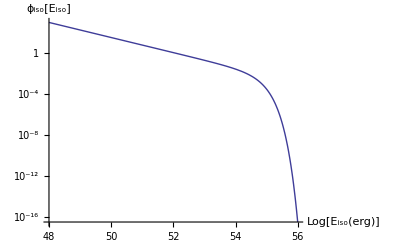

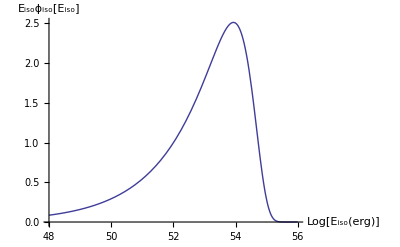

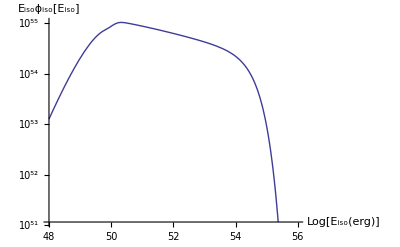

```mathematica
LogPlot[ϕiso[10^x],{x,48,56},PlotRange->Full,AxesLabel->{"Log[E_iso(erg)]","ϕ_iso[E_iso]"}]
Plot[10^x/10^52*ϕiso[10^x],{x,48,56},AxesLabel->{"Log[E_iso(erg)]","E_isoϕ_iso[E_iso]"}]
LogPlot[10^x*Averageϕiso7wp1CElow[x],{x,48,56},AxesLabel->{"Log[E_iso(erg)]","E_isoϕ_iso[E_iso]"}]
```

with z-7 chemical feedback

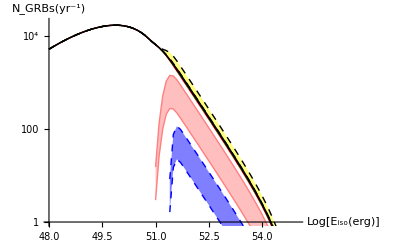

with z-7 chemical feedback

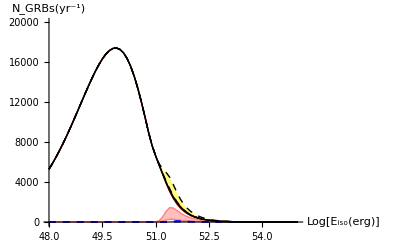

```mathematica
"with z-7 chemical feedback"
Show[ListLogPlot[Aveϕiso7wp1CEtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListLogPlot[Aveϕiso7sp1CEtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListLogPlot[{Aveϕiso7wp3CEtableup,Aveϕiso7wp3CEtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListLogPlot[{Aveϕiso7wCEtableup,Aveϕiso7wCEtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListLogPlot[{Aveϕiso7sp3CEtableup,Aveϕiso7sp3CEtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListLogPlot[{Aveϕiso7sCEtableup,Aveϕiso7sCEtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{Log[1],Log[20000]}},AxesOrigin->{48,Log[1]}] 
 "with z-7 chemical feedback"
Show[ListPlot[Aveϕiso7wp1CEtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListPlot[Aveϕiso7sp1CEtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListPlot[{Aveϕiso7wp3CEtableup,Aveϕiso7wp3CEtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListPlot[{Aveϕiso7wCEtableup,Aveϕiso7wCEtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListPlot[{Aveϕiso7sp3CEtableup,Aveϕiso7sp3CEtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListPlot[{Aveϕiso7sCEtableup,Aveϕiso7sCEtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{0,20000}},AxesOrigin->{48,0}]
```

with z-17 chemical feedback

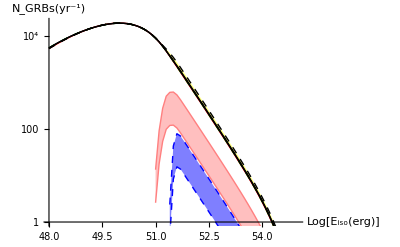

with z-17 chemical feedback

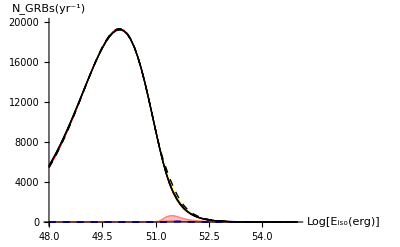

```mathematica
"with z-17 chemical feedback"
Show[ListLogPlot[Aveϕiso17wp1CEtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListLogPlot[Aveϕiso17sp1CEtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListLogPlot[{Aveϕiso17wp3CEtableup,Aveϕiso17wp3CEtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListLogPlot[{Aveϕiso17wCEtableup,Aveϕiso17wCEtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListLogPlot[{Aveϕiso17sp3CEtableup,Aveϕiso17sp3CEtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListLogPlot[{Aveϕiso17sCEtableup,Aveϕiso17sCEtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{Log[1],Log[20000]}},AxesOrigin->{48,Log[1]}] 
 "with z-17 chemical feedback"
Show[ListPlot[Aveϕiso17wp1CEtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListPlot[Aveϕiso17sp1CEtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListPlot[{Aveϕiso17wp3CEtableup,Aveϕiso17wp3CEtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListPlot[{Aveϕiso17wCEtableup,Aveϕiso17wCEtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListPlot[{Aveϕiso17sp3CEtableup,Aveϕiso17sp3CEtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListPlot[{Aveϕiso17sCEtableup,Aveϕiso17sCEtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{0,20000}},AxesOrigin->{48,0}]
```

with z-7 chemical feedback

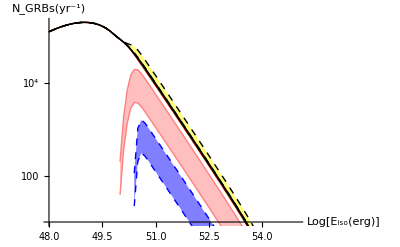

with z-7 chemical feedback

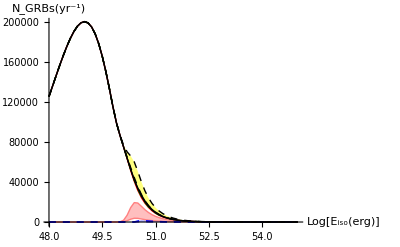

with z-17 chemical feedback

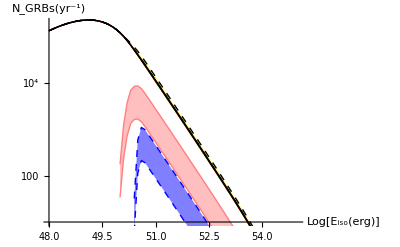

with z-17 chemical feedback

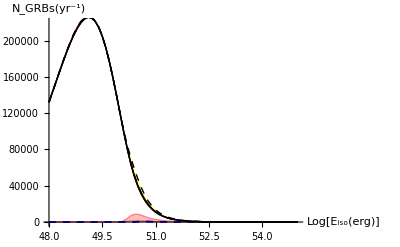

```mathematica
"with z-7 chemical feedback"
Show[ListLogPlot[Aveϕiso7wp1CElowtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListLogPlot[Aveϕiso7sp1CElowtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListLogPlot[{Aveϕiso7wp3CElowtableup,Aveϕiso7wp3CElowtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListLogPlot[{Aveϕiso7wCElowtableup,Aveϕiso7wCElowtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListLogPlot[{Aveϕiso7sp3CElowtableup,Aveϕiso7sp3CElowtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListLogPlot[{Aveϕiso7sCElowtableup,Aveϕiso7sCElowtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{Log[10],Log[200000]}},AxesOrigin->{48,Log[10]}] 
 "with z-7 chemical feedback"
Show[ListPlot[Aveϕiso7wp1CElowtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListPlot[Aveϕiso7sp1CElowtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListPlot[{Aveϕiso7wp3CElowtableup,Aveϕiso7wp3CElowtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListPlot[{Aveϕiso7wCElowtableup,Aveϕiso7wCElowtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListPlot[{Aveϕiso7sp3CElowtableup,Aveϕiso7sp3CElowtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListPlot[{Aveϕiso7sCElowtableup,Aveϕiso7sCElowtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{0,200000}},AxesOrigin->{48,0}] 
 "with z-17 chemical feedback"
Show[ListLogPlot[Aveϕiso17wp1CElowtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListLogPlot[Aveϕiso17sp1CElowtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListLogPlot[{Aveϕiso17wp3CElowtableup,Aveϕiso17wp3CElowtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListLogPlot[{Aveϕiso17wCElowtableup,Aveϕiso17wCElowtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListLogPlot[{Aveϕiso17sp3CElowtableup,Aveϕiso17sp3CElowtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListLogPlot[{Aveϕiso17sCElowtableup,Aveϕiso17sCElowtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{Log[10],Log[200000]}},AxesOrigin->{48,Log[10]}] 
 "with z-17 chemical feedback"
Show[ListPlot[Aveϕiso17wp1CElowtable,PlotStyle->Red,PlotRange->Full,Joined->True],
ListPlot[Aveϕiso17sp1CElowtable,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListPlot[{Aveϕiso17wp3CElowtableup,Aveϕiso17wp3CElowtabledown},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListPlot[{Aveϕiso17wCElowtableup,Aveϕiso17wCElowtabledown},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListPlot[{Aveϕiso17sp3CElowtableup,Aveϕiso17sp3CElowtabledown},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListPlot[{Aveϕiso17sCElowtableup,Aveϕiso17sCElowtabledown},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","N_GRBs(yr^-1)"},PlotRange->{{48,55},{0,220000}},AxesOrigin->{48,0}]
```

norm with z-7 chemical feedback

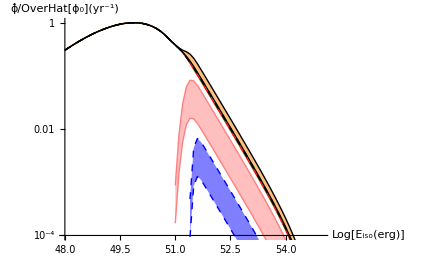

norm with z-7 chemical feedback

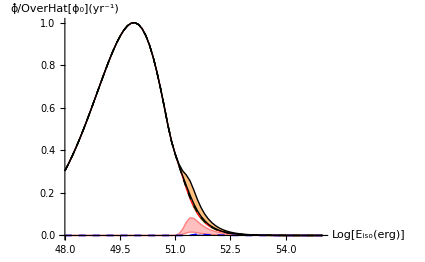

norm with z-17 chemical feedback

-Graphics-

norm with z-17 chemical feedback

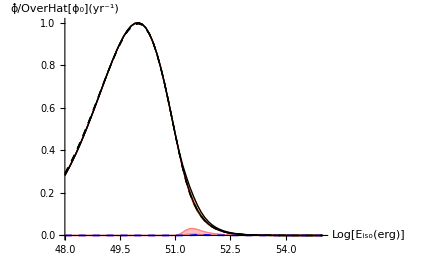

```mathematica
"norm with z-7 chemical feedback"
Show[ListLogPlot[Aveϕiso7wp1CEtablenorm,PlotStyle->Red,PlotRange->Full,Joined->True],
ListLogPlot[Aveϕiso7sp1CEtablenorm,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListLogPlot[{Aveϕiso7wp3CEtableupnorm,Aveϕiso7wp3CEtabledownnorm},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListLogPlot[{Aveϕiso7sCEtableupnorm,Aveϕiso7sCEtabledownnorm},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListLogPlot[{Aveϕiso7sp3CEtableupnorm,Aveϕiso7sp3CEtabledownnorm},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListLogPlot[{Aveϕiso7wCEtableupnorm,Aveϕiso7wCEtabledownnorm},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","ϕ̂/OverHat[ϕ_0](yr^-1)"},PlotRange->{{48,55},{Log[0.0001],Log[1]}},AxesOrigin->{48,Log[0.0001]}] 
 "norm with z-7 chemical feedback"
Show[ListPlot[Aveϕiso7wp1CEtablenorm,PlotStyle->Red,PlotRange->Full,Joined->True],
ListPlot[Aveϕiso7sp1CEtablenorm,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListPlot[{Aveϕiso7wp3CEtableupnorm,Aveϕiso7wp3CEtabledownnorm},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListPlot[{Aveϕiso7sCEtableupnorm,Aveϕiso7sCEtabledownnorm},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListPlot[{Aveϕiso7sp3CEtableupnorm,Aveϕiso7sp3CEtabledownnorm},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListPlot[{Aveϕiso7wCEtableupnorm,Aveϕiso7wCEtabledownnorm},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","ϕ̂/OverHat[ϕ_0](yr^-1)"},PlotRange->{{48,55},{0,1}},AxesOrigin->{48,0}] 
 "norm with z-17 chemical feedback"
Show[ListLogPlot[Aveϕiso17wp1CEtablenorm,PlotStyle->Red,PlotRange->Full,Joined->True],
ListLogPlot[Aveϕiso17sp1CEtablenorm,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListLogPlot[{Aveϕiso17wp3CEtableupnorm,Aveϕiso17wp3CEtabledownnorm},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListLogPlot[{Aveϕiso17sCEtableupnorm,Aveϕiso17sCEtabledownnorm},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListLogPlot[{Aveϕiso17sp3CEtableupnorm,Aveϕiso17sp3CEtabledownnorm},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListLogPlot[{Aveϕiso17wCEtableupnorm,Aveϕiso17wCEtabledownnorm},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","ϕ̂/OverHat[ϕ_0](yr^-1)"},PlotRange->{{48,55},{Log[0.0001],Log[1]}},AxesOrigin->{48,Log[0.0001]}] 
 "norm with z-17 chemical feedback"
Show[ListPlot[Aveϕiso17wp1CEtablenorm,PlotStyle->Red,PlotRange->Full,Joined->True],
ListPlot[Aveϕiso17sp1CEtablenorm,Joined->True,PlotStyle->{Green,Dashed},PlotRange->Full],ListPlot[{Aveϕiso17wp3CEtableupnorm,Aveϕiso17wp3CEtabledownnorm},PlotStyle->Pink,PlotRange->Full,Filling->{1->{2}},Joined->True,FillingStyle->Directive[Opacity[0.5],Pink]],
ListPlot[{Aveϕiso17sCEtableupnorm,Aveϕiso17sCEtabledownnorm},Joined->True,PlotStyle->{{Black,Dashed},{Black,Dashed}},PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Yellow]],
ListPlot[{Aveϕiso17sp3CEtableupnorm,Aveϕiso17sp3CEtabledownnorm},PlotStyle->{{Blue,Dashed},{Blue,Dashed}},Joined->True,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Blue]],ListPlot[{Aveϕiso17wCEtableupnorm,Aveϕiso17wCEtabledownnorm},Joined->True,PlotStyle->Black,PlotRange->Full,Filling->{1->{2}},FillingStyle->Directive[Opacity[0.5],Orange]],AxesLabel->{"Log[E_iso(erg)]","ϕ̂/OverHat[ϕ_0](yr^-1)"},PlotRange->{{48,55},{0,1}},AxesOrigin->{48,0}]
```